## Archived code

```mathematica
(*
(* findSym is Implemented from Jens *)
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; 
(* we subtract from each point the center of mass. 
This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids.
 We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of two coordinates,
 which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)
(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},
{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},
{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]
];
{centerOfMass,v1,v2}
]
*)
```

### mask to region/shortest tour for boundary

```mathematica
(*
(*given a mask -> find shortest tour and convert to region *)
convertToRegion[mask_]:= Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos= PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered = Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
]
*)
```

### bisect region

```mathematica
(*
bisectReg[mask_, options_:False]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,pt1,pt2,list,
trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask,imgDim1, imgDim2},
{imgDim1,imgDim2}=ImageDimensions@mask;

{centerofMass,v1,v2} = findSym[mask];
{pixelordered,ℛ1}=convertToRegion[mask];
ℛ2=InfiniteLine[{centerofMass,centerofMass+v2}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[options, Print@Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],
Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]]
];

Join[{centerofMass},pt1,pt2]
]
*)
```

### Bresenham Line

```mathematica
(*
bresenhamLine[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]
];
*)
```

### Axis of elongation

```mathematica
(*
axisElongation[mask_,div_:5]:=Block[{centroid,pt1,pt2,boundary,tour,boundaryc,nF,ℛ1,ℛ2,
intersections,rotationTransform,pts,θ,r,infinitelines,contour,surfacepts,pos,surfacepts2,
diameter,p,maxD},{centroid,pt1,pt2}=bisectReg@mask;
boundary=PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[boundary];
boundaryc=Part[boundary,tour];
nF=Nearest[boundaryc]; (* Nearest Function *)
ℛ1=BoundaryMeshRegion[boundary,Line@tour]; (* boundary *)
ℛ2=InfiniteLine[{centroid,pt1}]; (* pseudo axis of symmetry *)
intersections=Cases[RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1],_Point]/.Point[{x_}]:> x;rotationTransform=RotationTransform[div Degree,centroid];pts=Rest@NestList[rotationTransform,pt1,360/(div*2)];infinitelines=InfiniteLine[{centroid,#}]&/@pts;contour= Polygon@boundaryc;surfacepts = Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],contour,#}]]&/@infinitelines;pos = Position[surfacepts,_?(Length@#>2&),{1}];surfacepts2=MapAt[Sequence@@TakeLargestBy[Permutations[#,{2}],EuclideanDistance[#[[1]],#[[2]]]&,1]&,surfacepts,pos];
MaximalBy[surfacepts2,Apply[EuclideanDistance]]
]
*)
```

### Axis readout

```mathematica
(*
axesReadout[mask_]:=Block[{pts,imgPeripts,nf,ptsB,perms,extrema,pointsL,subdiv},
pts=bisectMask[mask];
imgPeripts=First@@Values@ComponentMeasurements[mask,"PerimeterPositions"];
nf=Nearest[imgPeripts];
ptsB={Round@*First@pts}~Join~Flatten[Round@*nf/@Rest[pts],1];
perms=Permutations[ptsB,{2}];
extrema = Extract[perms,FirstPosition[#,Max@#]&[N@EuclideanDistance[Sequence@@#]&/@perms]];
pointsL=bresenhamLine[First@extrema,Last@extrema];
subdiv=N@Subdivide[Length@pointsL];
{subdiv,pointsL}
];
*)
```

## Spatial density gradients

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\spatial density aggregates\\axesProp.m";
```

```mathematica
(* ImageTake[img,{128,717},{636,1429}] for image crop: deprecate after getting original images *)
```

```mathematica
With[{x="39"},
mask=Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@density\\"<>x<>"\\Mask.tif"];
imgN=ImageAdjust@ColorConvert[Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@density\\"<>x<>"\\"<>x<>" - Nuc.tif"],"Grayscale"];
imgB=ImageAdjust@ColorConvert[Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@density\\"<>x<>"\\"<>x<>" - Brach.tif"],"Grayscale"];
]
```

```mathematica
{length,pointsL}=bresenhamVector[mask];
```

```mathematica
elongVec=elongationVector[mask]/.{x_}:> x
```

{{545.191,237.},{814.527,796.473}}

```mathematica
VectorAngle[Last@pointsL-First@pointsL,Last@elongVec-First@elongVec]*180/Pi
```

4.9381

```mathematica
Row[
{Show[mask,Graphics[{Blue,Line@pointsL}],ImageSize-> Medium],
Show[HighlightImage[imgN,{Darker@Green,FaceForm[],mask},"Darken"],
Graphics[{GrayLevel[0.1],Arrow[{First@pointsL,Last@pointsL}],
Cyan,Opacity[0.6],Arrow@elongVec}],ImageSize-> Medium]}
]
```

-Graphics--Graphics-

```mathematica
(* Arrow shows the direction in which the signal is read - however, the standard is to read from low nuclei density
 to high nuclei density region. Reverse read values if necessary *)
```

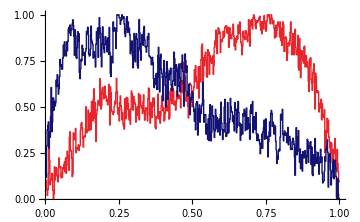

```mathematica
ListStepPlot[{Thread[{Rest@length,Rescale@ImageValue[imgN,pointsL]}],
Thread[{Rest@length,Rescale@ImageValue[imgB,pointsL]}]},
PlotStyle->{{Thick,RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144]},{Thick,RGBColor[0.07924700513978256, 0.07394564469935314, 0.4499539624003866]}},Joined-> True,ImageSize->Medium]
```

## Plot

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\spatial density aggregates\\savedDat.mx";
```

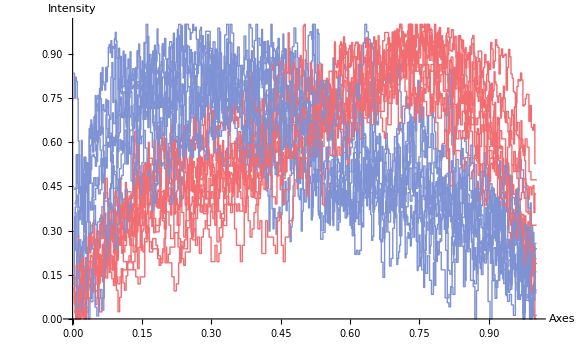

```mathematica
plt1=Show[ListStepPlot[#,PlotRange->Full,PlotStyle->{{Thin,Nest[Lighter,RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144],1]},
{Thin,Nest[Lighter,RGBColor[0.24945963759122658, 0.3599225889198605, 0.7438707897882956],1]}},ImageSize->Large]&/@savedData,
AxesStyle->{{FontSize-> 15},{FontSize-> 15}},AxesLabel-> {"Axes","Intensity"}]
```

```mathematica
mean=(Mean/@(Flatten[BinLists[Flatten[savedData[[All,#]],1],0.01,100],1]/.{}-> Sequence[]))&/@Range@2;
```

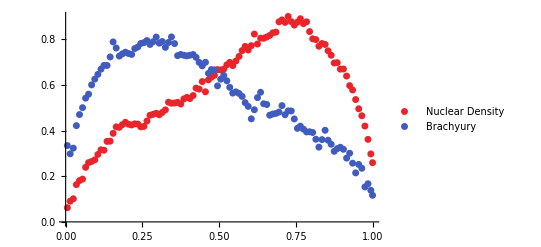

```mathematica
plt2=ListPlot[mean,PlotStyle->{{PointSize[0.0125],RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144]},
{PointSize[0.0125],RGBColor[0.24945963759122658, 0.3599225889198605, 0.7438707897882956]}},PlotLegends->{"Nuclear Density","Brachyury"}]
```

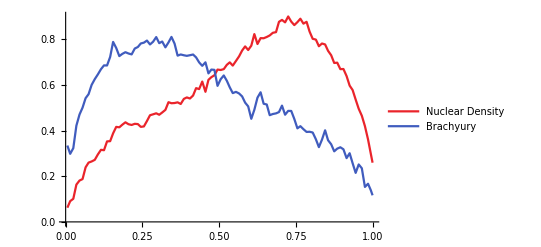

```mathematica
plt3=ListPlot[mean,PlotStyle->{{Thick,RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144]},{Thick,RGBColor[0.24945963759122658, 0.3599225889198605, 0.7438707897882956]}},
PlotLegends->{"Nuclear Density","Brachyury"},Joined->True]
```

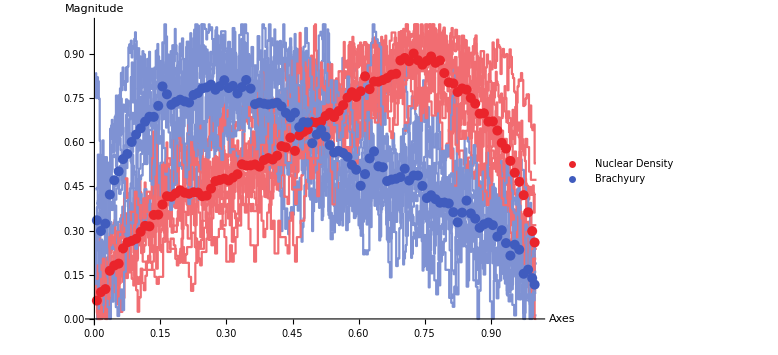

```mathematica
Show[plt1,plt2,AxesLabel-> {"Axes","Magnitude"}]
```

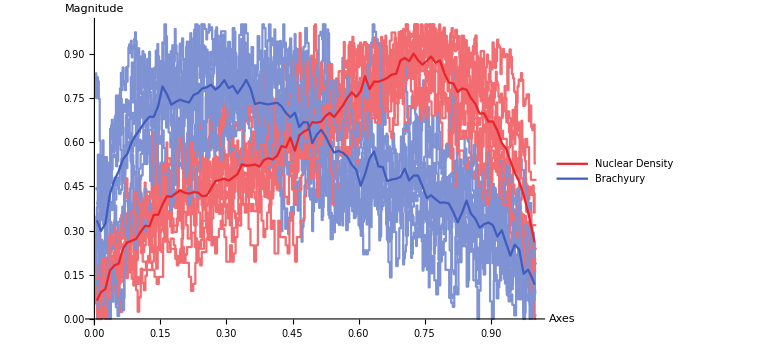

```mathematica
Show[plt1,plt3,AxesLabel-> {"Axes","Magnitude"}]
```

```mathematica
{u,v}=(StandardDeviation/@Flatten[Map[Last,BinLists[Flatten[savedData[[All,#]],1],0.01,100]/.
{}-> Sequence[],{3}],1])&/@Range[2];
```

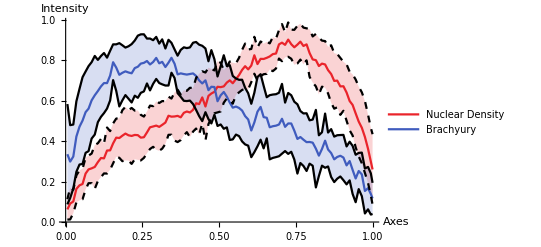

```mathematica
plt4=ListPlot[{mean[[1]],mean[[2]],Thread[{mean[[1]][[All,1]],mean[[1]][[All,2]]+u}],Thread[{mean[[1]][[All,1]],mean[[1]][[All,2]]-u}],
Thread[{mean[[2]][[All,1]],mean[[2]][[All,2]]+v}],Thread[{mean[[2]][[All,1]],mean[[2]][[All,2]]-v}]},PlotStyle->{{Thick,RGBColor[0.9184512028405248, 0.14170905749799229, 0.16848456616569144]},{Thick,RGBColor[0.24945963759122658, 0.3599225889198605, 0.7438707897882956]},{Thick,Dashed,Black},{Thick,Dashed,Black},{Thick,Black},{Thick,Black}},Joined->{True,True,True,True},Filling->{1->{3},1-> {4},2-> {5},2-> {6}},PlotLegends->{"Nuclear Density","Brachyury"},AxesStyle->{{FontSize-> 15},{FontSize-> 15}},AxesLabel-> {"Axes","Intensity"}]
```

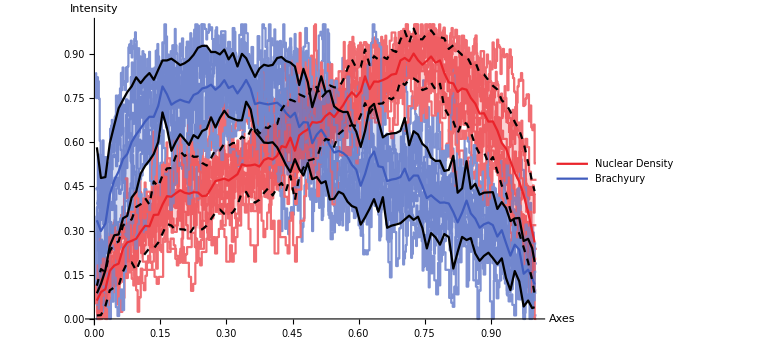

```mathematica
plt1~Show~plt4
```

### Angular difference between principle direction and elongation vector

```mathematica
pt={0.0475,0.1086,0.1578,4.9381,5.0329,5.0821,14.8902,20.1839,24.8426,24.9143};
```

```mathematica
qt=QuantityArray[pt,"Degrees"]
```

QuantityArray[…]

```mathematica
spread=Thread[{RandomReal[{0.55,0.85},Length@qt],qt}];
```

```mathematica
p=MapAt[QuantityMagnitude,spread,{All,2}];
```

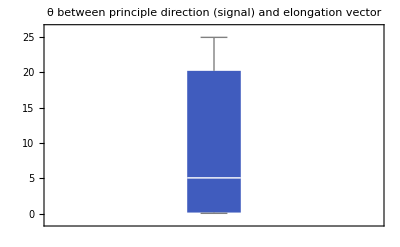

```mathematica
BoxWhiskerChart[qt,ChartStyle->RGBColor[0.24945963759122658, 0.3599225889198605, 0.7438707897882956],FrameTicksStyle->Directive[Gray,Bold,12],
PlotLabel->Style[#,Bold,Black]&@"θ between principle direction (signal) and elongation vector"]
```